## Numerators

## Algebra utilities

```mathematica
SetDirectory[NotebookDirectory[]]
<<"./tools/tensTools.m"
<<"./tools/ampTools2.1.m"
```

/Users/zeno/Desktop/LTD/program/alphaLoopMisc

The documented functions in this package are: 
 ?extractTensCoeff
 ?getSymNumericCoeff

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

## Numerators

### Numerator definitions

#### Double Triangle

```mathematica
dtNum[k_,l_,p1_,p2_]:=(
(-I  gamma[s[11],mu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I  gamma[s[13],mu2,s[14]] T[a[11],i[11],i[12]])
I vector[l,mu3]gamma[s[14],mu3,s[15]]
(-I  gamma[s[15],nu,s[16]])
I vector[l-p1-p2,mu4]gamma[s[16],mu4,s[17]]
(-I  gamma[s[17],mu2,s[18]] T[a[11],i[12],i[11]])
I vector[k-p1-p2,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

dtNumerator[k_,l_,p1_,p2_]=contractColor[contractSpin[dtNum[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

512 SP[k,p1] SP[k,p2] SP[l,l]-512 SP[k,l] SP[k,p2] SP[l,p1]-256 SP[k,p1] SP[k,p2] SP[l,p1]+256 SP[k,p2]^2 SP[l,p1]+256 SP[k,p2] SP[l,p1]^2-512 SP[k,l] SP[k,p1] SP[l,p2]+256 SP[k,p1]^2 SP[l,p2]-256 SP[k,p1] SP[k,p2] SP[l,p2]+512 SP[k,k] SP[l,p1] SP[l,p2]-256 SP[k,p1] SP[l,p1] SP[l,p2]-256 SP[k,p2] SP[l,p1] SP[l,p2]+256 SP[k,p1] SP[l,p2]^2+256 SP[k,l] SP[k,p2] SP[p1,p1]-256 SP[k,p2] SP[l,l] SP[p1,p1]-256 SP[k,k] SP[l,p2] SP[p1,p1]+256 SP[k,l] SP[l,p2] SP[p1,p1]+512 SP[k,p2] SP[l,p2] SP[p1,p1]+512 SP[k,l]^2 SP[p1,p2]-256 SP[k,l] SP[k,p1] SP[p1,p2]-256 SP[k,l] SP[k,p2] SP[p1,p2]-256 SP[k,k] SP[l,l] SP[p1,p2]-256 SP[k,l] SP[l,p1] SP[p1,p2]+512 SP[k,p1] SP[l,p1] SP[p1,p2]-256 SP[k,l] SP[l,p2] SP[p1,p2]+512 SP[k,p2] SP[l,p2] SP[p1,p2]-256 SP[k,l] SP[p1,p1] SP[p1,p2]+256 SP[k,l] SP[k,p1] SP[p2,p2]-256 SP[k,p1] SP[l,l] SP[p2,p2]-256 SP[k,k] SP[l,p1] SP[p2,p2]+256 SP[k,l] SP[l,p1] SP[p2,p2]+512 SP[k,p1] SP[l,p1] SP[p2,p2]-512 SP[k,l] SP[p1,p1] SP[p2,p2]-256 SP[k,l] SP[p1,p2] SP[p2,p2]

#### 2 to2 (with initial quarks)

```mathematica
twoNum[k_,l_,p1_,p2_,p_]:=(
(-I gamma[s[11],nu,s[12]])
 I vector[k+p1+p2,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu,s[14]])
I vector[k+p,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],mu2,s[16]]T[a[11],i[11],i[12]])
I vector[k+l+p,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]]T[a[11],i[12],i[11]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

twoNumerator[k_,l_,p1_,p2_,p_]=contractColor[contractSpin[twoNum[k,l,p1,p2,p],{k,l,p1,p2,p}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

-512 SP[k,k] SP[k,p1] SP[k,p2]-1024 SP[k,l] SP[k,p1] SP[k,p2]-1024 SP[k,p] SP[k,p1] SP[k,p2]-512 SP[k,p1] SP[k,p2] SP[l,p]+256 SP[k,k] SP[k,p2] SP[l,p1]+256 SP[k,p] SP[k,p2] SP[l,p1]+256 SP[k,k] SP[k,p1] SP[l,p2]+256 SP[k,p] SP[k,p1] SP[l,p2]-512 SP[k,p1] SP[k,p2] SP[p,p]-256 SP[k,l] SP[k,p2] SP[p,p1]-256 SP[k,l] SP[k,p1] SP[p,p2]-256 SP[k,k] SP[k,p2] SP[p1,p1]-512 SP[k,l] SP[k,p2] SP[p1,p1]-512 SP[k,p] SP[k,p2] SP[p1,p1]-256 SP[k,p2] SP[l,p] SP[p1,p1]+256 SP[k,k] SP[l,p2] SP[p1,p1]+256 SP[k,p] SP[l,p2] SP[p1,p1]-256 SP[k,p2] SP[p,p] SP[p1,p1]-256 SP[k,l] SP[p,p2] SP[p1,p1]-256 SP[k,k] SP[k,p1] SP[p1,p2]-512 SP[k,l] SP[k,p1] SP[p1,p2]-512 SP[k,p] SP[k,p1] SP[p1,p2]-256 SP[k,k] SP[k,p2] SP[p1,p2]-512 SP[k,l] SP[k,p2] SP[p1,p2]-512 SP[k,p] SP[k,p2] SP[p1,p2]-256 SP[k,p1] SP[l,p] SP[p1,p2]-256 SP[k,p2] SP[l,p] SP[p1,p2]+256 SP[k,k] SP[l,p1] SP[p1,p2]+256 SP[k,p] SP[l,p1] SP[p1,p2]+256 SP[k,k] SP[l,p2] SP[p1,p2]+256 SP[k,p] SP[l,p2] SP[p1,p2]-256 SP[k,p1] SP[p,p] SP[p1,p2]-256 SP[k,p2] SP[p,p] SP[p1,p2]-256 SP[k,l] SP[p,p1] SP[p1,p2]-256 SP[k,l] SP[p,p2] SP[p1,p2]-256 SP[k,k] SP[k,p1] SP[p2,p2]-512 SP[k,l] SP[k,p1] SP[p2,p2]-512 SP[k,p] SP[k,p1] SP[p2,p2]-256 SP[k,p1] SP[l,p] SP[p2,p2]+256 SP[k,k] SP[l,p1] SP[p2,p2]+256 SP[k,p] SP[l,p1] SP[p2,p2]-256 SP[k,p1] SP[p,p] SP[p2,p2]-256 SP[k,l] SP[p,p1] SP[p2,p2]

#### Bubble

```mathematica
bubNum[k_,l_,p1_,p2_,p_]:=(
(-I  gamma[s[11],nu,s[12]])
 I vector[k-p1-p2,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu,s[14]])
I vector[k,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],mu2,s[16]]T[a[11],i[11],i[12]])
I vector[l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]] T[a[11],i[12],i[11]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

bubNumerator[k_,l_,p1_,p2_,p_]=contractColor[contractSpin[bubNum[k,l,p1,p2,p],{k,l,p1,p2,p}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

-1024 SP[k,l] SP[k,p1] SP[k,p2]+256 SP[k,k] SP[k,p2] SP[l,p1]+256 SP[k,k] SP[k,p1] SP[l,p2]+512 SP[k,l] SP[k,p2] SP[p1,p1]-256 SP[k,k] SP[l,p2] SP[p1,p1]+512 SP[k,l] SP[k,p1] SP[p1,p2]+512 SP[k,l] SP[k,p2] SP[p1,p2]-256 SP[k,k] SP[l,p1] SP[p1,p2]-256 SP[k,k] SP[l,p2] SP[p1,p2]+512 SP[k,l] SP[k,p1] SP[p2,p2]-256 SP[k,k] SP[l,p1] SP[p2,p2]

#### 2 to 2 (with one initial gluon and one initial quark)

```mathematica
twoV2Num[k_,l_,p1_,p2_]:=(
(-I gamma[s[11],mu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu2,s[14]]T[a[11],i[11],i[12]])
I vector[l+p1+p2,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],nu,s[16]])
I vector[l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]]T[a[11],i[12],i[11]])
I vector[k+p1+p2,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

twoV2Numerator[k_,l_,p1_,p2_]=contractColor[contractSpin[twoV2Num[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

512 SP[k,p1] SP[k,p2] SP[l,l]-512 SP[k,l] SP[k,p2] SP[l,p1]+256 SP[k,p1] SP[k,p2] SP[l,p1]-256 SP[k,p2]^2 SP[l,p1]-256 SP[k,p2] SP[l,p1]^2-512 SP[k,l] SP[k,p1] SP[l,p2]-256 SP[k,p1]^2 SP[l,p2]+256 SP[k,p1] SP[k,p2] SP[l,p2]+512 SP[k,k] SP[l,p1] SP[l,p2]+256 SP[k,p1] SP[l,p1] SP[l,p2]+256 SP[k,p2] SP[l,p1] SP[l,p2]-256 SP[k,p1] SP[l,p2]^2-256 SP[k,l] SP[k,p2] SP[p1,p1]+256 SP[k,p2] SP[l,l] SP[p1,p1]+256 SP[k,k] SP[l,p2] SP[p1,p1]-256 SP[k,l] SP[l,p2] SP[p1,p1]+512 SP[k,l]^2 SP[p1,p2]+256 SP[k,l] SP[k,p1] SP[p1,p2]+256 SP[k,l] SP[k,p2] SP[p1,p2]-256 SP[k,k] SP[l,l] SP[p1,p2]+256 SP[k,l] SP[l,p1] SP[p1,p2]+256 SP[k,l] SP[l,p2] SP[p1,p2]+256 SP[k,l] SP[p1,p1] SP[p1,p2]+512 SP[k,l] SP[p1,p2]^2-256 SP[k,l] SP[k,p1] SP[p2,p2]+256 SP[k,p1] SP[l,l] SP[p2,p2]+256 SP[k,k] SP[l,p1] SP[p2,p2]-256 SP[k,l] SP[l,p1] SP[p2,p2]+256 SP[k,l] SP[p1,p2] SP[p2,p2]

#### 2 to2 s - channel

```mathematica
sChannelBubNum[k_,l_,p1_,p2_]:=(
(-I gamma[s[11],nu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu,s[14]])
I vector[k+p1+p2,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],mu2,s[16]]T[a[11],i[11],i[12]])
I vector[k+p1+p2-l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]]T[a[11],i[12],i[11]])
I vector[k+p1+p2,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

sChannelBubNumerator[k_,l_,p1_,p2_]=contractColor[contractSpin[sChannelBubNum[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

-512 SP[k,k] SP[k,p1] SP[k,p2]+1024 SP[k,l] SP[k,p1] SP[k,p2]-1024 SP[k,p1]^2 SP[k,p2]-1024 SP[k,p1] SP[k,p2]^2-256 SP[k,k] SP[k,p2] SP[l,p1]+512 SP[k,p1] SP[k,p2] SP[l,p1]-512 SP[k,p2]^2 SP[l,p1]-256 SP[k,k] SP[k,p1] SP[l,p2]-512 SP[k,p1]^2 SP[l,p2]+512 SP[k,p1] SP[k,p2] SP[l,p2]-256 SP[k,k] SP[k,p2] SP[p1,p1]+512 SP[k,l] SP[k,p2] SP[p1,p1]-1024 SP[k,p1] SP[k,p2] SP[p1,p1]-512 SP[k,p2]^2 SP[p1,p1]+256 SP[k,p2] SP[l,p1] SP[p1,p1]-256 SP[k,p1] SP[l,p2] SP[p1,p1]+512 SP[k,p2] SP[l,p2] SP[p1,p1]-256 SP[k,p2] SP[p1,p1]^2-256 SP[k,k] SP[k,p1] SP[p1,p2]+512 SP[k,l] SP[k,p1] SP[p1,p2]-512 SP[k,p1]^2 SP[p1,p2]-256 SP[k,k] SP[k,p2] SP[p1,p2]+512 SP[k,l] SP[k,p2] SP[p1,p2]-2048 SP[k,p1] SP[k,p2] SP[p1,p2]-512 SP[k,p2]^2 SP[p1,p2]+512 SP[k,p1] SP[l,p1] SP[p1,p2]+512 SP[k,p2] SP[l,p2] SP[p1,p2]-256 SP[k,p1] SP[p1,p1] SP[p1,p2]-768 SP[k,p2] SP[p1,p1] SP[p1,p2]-512 SP[k,p1] SP[p1,p2]^2-512 SP[k,p2] SP[p1,p2]^2-256 SP[k,k] SP[k,p1] SP[p2,p2]+512 SP[k,l] SP[k,p1] SP[p2,p2]-512 SP[k,p1]^2 SP[p2,p2]-1024 SP[k,p1] SP[k,p2] SP[p2,p2]+512 SP[k,p1] SP[l,p1] SP[p2,p2]-256 SP[k,p2] SP[l,p1] SP[p2,p2]+256 SP[k,p1] SP[l,p2] SP[p2,p2]-256 SP[k,p1] SP[p1,p1] SP[p2,p2]-256 SP[k,p2] SP[p1,p1] SP[p2,p2]-768 SP[k,p1] SP[p1,p2] SP[p2,p2]-256 SP[k,p2] SP[p1,p2] SP[p2,p2]-256 SP[k,p1] SP[p2,p2]^2

#### 2 to 2 u - channel

```mathematica
uChannelNum[k_,l_,p1_,p2_]:=(
(-I gamma[s[11],mu,s[12]])
 I vector[k+p1+p2,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu2,s[14]])
I vector[k+l+p1+p2,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],nu,s[16]])
I vector[k+l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

uChannelNumerator[k_,l_,p1_,p2_]=contractColor[contractSpin[uChannelNum[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

128 SP[k,p1] SP[k,p2] SP[l,l]-128 SP[k,l] SP[k,p2] SP[l,p1]-64 SP[k,p2] SP[l,p1]^2-128 SP[k,l] SP[k,p1] SP[l,p2]+128 SP[k,k] SP[l,p1] SP[l,p2]+64 SP[k,p1] SP[l,p1] SP[l,p2]+64 SP[k,p2] SP[l,p1] SP[l,p2]-64 SP[k,p1] SP[l,p2]^2+128 SP[k,p2]^2 SP[p1,p1]+64 SP[k,p2] SP[l,l] SP[p1,p1]-64 SP[k,l] SP[l,p2] SP[p1,p1]+128 SP[k,p2] SP[l,p2] SP[p1,p1]+64 SP[k,k]^2 SP[p1,p2]+128 SP[k,k] SP[k,l] SP[p1,p2]+128 SP[k,l]^2 SP[p1,p2]+128 SP[k,k] SP[k,p1] SP[p1,p2]+128 SP[k,l] SP[k,p1] SP[p1,p2]+128 SP[k,p1]^2 SP[p1,p2]+128 SP[k,k] SP[k,p2] SP[p1,p2]+128 SP[k,l] SP[k,p2] SP[p1,p2]+128 SP[k,p2]^2 SP[p1,p2]-64 SP[k,k] SP[l,l] SP[p1,p2]+64 SP[k,k] SP[l,p1] SP[p1,p2]+64 SP[k,l] SP[l,p1] SP[p1,p2]+128 SP[k,p1] SP[l,p1] SP[p1,p2]+64 SP[k,k] SP[l,p2] SP[p1,p2]+64 SP[k,l] SP[l,p2] SP[p1,p2]+128 SP[k,p2] SP[l,p2] SP[p1,p2]-64 SP[k,k] SP[p1,p1] SP[p1,p2]-64 SP[k,l] SP[p1,p1] SP[p1,p2]+128 SP[k,p1]^2 SP[p2,p2]+64 SP[k,p1] SP[l,l] SP[p2,p2]-64 SP[k,l] SP[l,p1] SP[p2,p2]+128 SP[k,p1] SP[l,p1] SP[p2,p2]-128 SP[k,k] SP[p1,p1] SP[p2,p2]-128 SP[k,l] SP[p1,p1] SP[p2,p2]-64 SP[k,k] SP[p1,p2] SP[p2,p2]-64 SP[k,l] SP[p1,p2] SP[p2,p2]

### Scalar product, norm, tensor definitions

```mathematica
SP[k_,q_]:=k[[1]]q[[1]]-k[[2]]q[[2]]-k[[3]]q[[3]]-k[[4]]q[[4]]
norm[k_]:=Sqrt[k[[2]]^2+k[[3]]^2+k[[4]]^2]
vector[k_,mu_]:=k[[mu]]
g[mu_,nu_]:=-KroneckerDelta[mu,nu]+2 KroneckerDelta[mu,0]KroneckerDelta[nu,0]
```

### Tests

#### Double triangle, u - channel and st - channel equivalences

Numerators of cut diagrams obtained from the same vacuum bubble are the same up to re-routing

```mathematica
Simplify[dtNumerator[{k0,kx,ky,kz},-{l0,lx,ly,lz}-{q0,qx,qy,qz},-{q0,qx,qy,qz},1,1]-twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]]
```

-16 (k0^2-kx^2-ky^2-kz^2) l0^2+32 k0 l0 (k0 l0-kx lx-ky ly-kz lz)-16 k0^2 (l0^2-lx^2-ly^2-lz^2)-8 (k0^2-kx^2-ky^2-kz^2) (l0^2-lx^2-ly^2-lz^2)-16 (k0^2-kx^2-ky^2-kz^2) l0 q0+16 k0 (k0 l0-kx lx-ky ly-kz lz) q0+16 l0 (k0 l0-kx lx-ky ly-kz lz) q0-16 k0 (l0^2-lx^2-ly^2-lz^2) q0+16 k0 l0 (k0 q0-kx qx-ky qy-kz qz)-16 l0^2 (k0 q0-kx qx-ky qy-kz qz)-8 (l0^2-lx^2-ly^2-lz^2) (k0 q0-kx qx-ky qy-kz qz)-16 k0^2 (l0 q0-lx qx-ly qy-lz qz)-8 (k0^2-kx^2-ky^2-kz^2) (l0 q0-lx qx-ly qy-lz qz)+16 k0 l0 (l0 q0-lx qx-ly qy-lz qz)-8 (k0 l0-kx lx-ky ly-kz lz) (q0^2-qx^2-qy^2-qz^2)+dtNumerator[{k0,kx,ky,kz},{-l0-q0,-lx-qx,-ly-qy,-lz-qz},{-q0,-qx,-qy,-qz},1,1]

```mathematica
Simplify[dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]-uChannelNumerator[{k0,kx,ky,kz}-{q0,qx,qy,qz},{l0,lx,ly,lz}-{k0,kx,ky,kz},{q0,qx,qy,qz},1,1]]
```

-8 (-3 ky^2 l0^2-3 kz^2 l0^2+ky^2 lx^2+kz^2 lx^2+ky^2 ly^2+kz^2 ly^2+ky^2 lz^2+kz^2 lz^2+3 ky^2 l0 q0+3 kz^2 l0 q0-2 ky l0 ly q0-2 kz l0 lz q0+3 ky ly q0^2+3 kz lz q0^2-ky^2 lx qx-kz^2 lx qx-ky ly qx^2-kz lz qx^2+3 ky l0^2 qy-ky lx^2 qy-ky^2 ly qy-kz^2 ly qy-ky ly^2 qy-ky lz^2 qy-4 ky l0 q0 qy+2 ky lx qx qy+ky ly qy^2-kz lz qy^2+3 kz l0^2 qz-kz lx^2 qz-kz ly^2 qz-ky^2 lz qz-kz^2 lz qz-kz lz^2 qz-4 kz l0 q0 qz+2 kz lx qx qz+2 kz ly qy qz+2 ky lz qy qz-ky ly qz^2+kz lz qz^2+kx^2 (-3 l0^2+lx^2+ly^2+lz^2+3 l0 q0-lx qx-ly qy-lz qz)+k0 (4 kz l0 lz-l0^2 q0+3 lx^2 q0+3 ly^2 q0-2 kz lz q0+3 lz^2 q0+l0 q0^2-2 l0 lx qx-4 lx q0 qx+3 l0 qx^2+kx (4 l0 lx-2 lx q0-2 l0 qx)-2 l0 ly qy-4 ly q0 qy+3 l0 qy^2+ky (4 l0 ly-2 ly q0-2 l0 qy)-2 kz l0 qz-2 l0 lz qz-4 lz q0 qz+3 l0 qz^2)+k0^2 (l0^2-l0 q0-3 (lx^2+ly^2+lz^2-lx qx-ly qy-lz qz))-kx (-3 l0^2 qx+lx^2 qx+2 l0 q0 (lx+2 qx)+qx (ly^2+lz^2-2 ly qy-2 lz qz)+lx (-3 q0^2-qx^2+qy^2+qz^2)))+dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]

#### Bubble correction, s - channel and t - channel equivalences

Numerators of cut diagrams obtained from the same vacuum bubble are the same up to re - routing

```mathematica
Simplify[bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-sChannelBubNumerator[{k0,kx,ky,kz}-{q0,qx,qy,qz},-{l0,lx,ly,lz}+{k0,kx,ky,kz},{q0,qx,qy,qz},1,1]]
```

0

```mathematica
Simplify[bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz}-{k0,kx,ky,kz},{0,0,0,0},-{q0,qx,qy,qz},1,1]]
```

0

## Testing ideas

## Testing the flow

-Graphics-

### Flow solutions

```mathematica
tTchUsual[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]-norm[{0,kx,ky,kz}-{0,lx,ly,lz}]+norm[{0,lx,ly,lz}])
```

```mathematica
tTchWeird[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}])
```

One thing to remember is that for more complicated cases (not for 1 parton + q -> 2 partons), the scaling is not always ensured to be positive (or have a well - defined sign), as the denominator is a difference of norms. In this case one has to add an heaviside theta

### Dirac delta jacobians

```mathematica
usualTchDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]-norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

weirdTchDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Toy integrand

-Graphics-

```mathematica
fWeird[kx_,ky_,kz_,lx_,ly_,lz_]:=Exp[-norm[{0,kx,ky,kz}]^2-norm[{0,lx,ly,lz}]^2]/(2norm[{0,kx,ky,kz}]2norm[{0,kx,ky,kz}-{0,lx,ly,lz}](norm[{0,kx,ky,kz}]-norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}])(norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]))
```

-Graphics-

```mathematica
fUsual[kx_,ky_,kz_,lx_,ly_,lz_]:=Exp[-norm[{0,kx,ky,kz}]^2-norm[{0,lx,ly,lz}]^2]/(2norm[{0,lx,ly,lz}]2norm[{0,kx,ky,kz}-{0,lx,ly,lz}](norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}]-norm[{0,kx,ky,kz}-{0,lx,ly,lz}])(-norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}]-norm[{0,kx,ky,kz}-{0,lx,ly,lz}]))
```

### Singular structure of Toy integrand

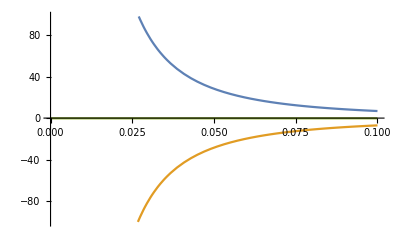

```mathematica
Plot[{fWeird[0,eps,0.5,0,0,1],fUsual[0,eps,0.5,0,0,1],fWeird[0,eps,0.5,0,0,1]+fUsual[0,eps,0.5,0,0,1]},{eps,0,0.1}]
```

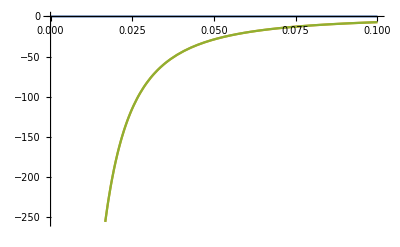

```mathematica
Plot[{fWeird[0,eps,-0.5,0,0,1],fUsual[0,eps,-0.5,0,0,1],fWeird[0,eps,-0.5,0,0,1]+fUsual[0,eps,-0.5,0,0,1]},{eps,0,0.1}]
```

### LU representation of Toy integrand

```mathematica
thF[x_]:=If[x>0,1,0];
```

```mathematica
sum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_]:=Module[{vt,rt,sumo},
vt=tTchUsual[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rt=tTchWeird[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

sumo=( vt^6 thF[vt](Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])fUsual[vt kx,vt ky,vt kz,vt lx,vt ly,vt lz]+rt^6 thF[rt](Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])fWeird[rt kx,rt ky,rt kz,rt lx,rt ly,rt lz]);

sumo/(Sqrt[Pi]sigma)
]
```

```mathematica
usualCutTot[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_]:=Module[{vt,sumo},
vt=tTchUsual[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

sumo=vt^6 thF[vt](Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])fUsual[vt kx,vt ky,vt kz,vt lx,vt ly,vt lz];

sumo/(Sqrt[Pi]sigma)
]

weirdCutTot[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_]:=Module[{rt,sumo},
rt=tTchWeird[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

sumo=rt^6 thF[rt](Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])fWeird[rt kx,rt ky,rt kz,rt lx,rt ly,rt lz];

sumo/(Sqrt[Pi]sigma)
]
```

```mathematica
sum[0,0.5,1,0,0,-0.5,1,0,0,1,1,0,0,-1,0.1];
```

General::munfl: Exp[-293847.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4407.7] is too small to represent as a normalized machine number; precision may be lost.

### Cancellations of IR singularities in the Toy model

This singularity is the only one with support, and thus subject to cancellation

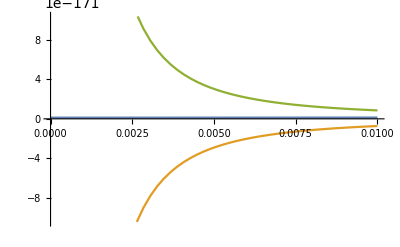

```mathematica
Plot[{sum[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.1],usualCutTot[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.1], weirdCutTot[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.1]},{eps,0,0.01}]
```

This singularity is the one without support, and actually corresponds to the limit t -> Infinity, with is suppressed exponentially by the h function

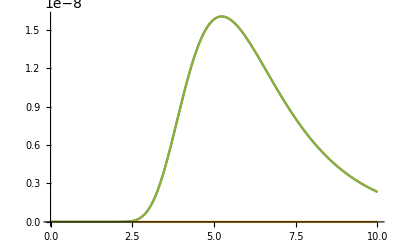

```mathematica
Plot[{sum[0,eps,1,0,0,0.5,1,0,0,1,1,0,0,-1,0.1],usualCutTot[0,eps,1,0,0,0.5,1,0,0,1,1,0,0,-1,0.1], weirdCutTot[0,eps,1,0,0,0.5,1,0,0,1,1,0,0,-1,0.1](*,1/(0.5-norm[{0,0,eps,0.5}]-norm[{0,0,eps,1}])*)},{eps,0,10}(*,PlotRange->All*)]
```

### Integration of Toy model integrand for varying h - function spread

```mathematica
(*Table[NIntegrate[sum[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,0.2],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->10^(i),MaxRecursion->1000],{i,1,8}]*)
```

NIntegrate::maxp: The integral failed to converge after 100 integrand evaluations. NIntegrate obtained 0.17304 and 0.0619169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300 integrand evaluations. NIntegrate obtained 0.392086 and 0.0700208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.336917 and 0.0459864 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0.17304,0.392086,0.336917,0.279555,0.272835,0.292462,0.313095,0.320344}

```mathematica
(*Table[NIntegrate[sum[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,0.5],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->10^(i),MaxRecursion->1000],{i,1,8}]*)
```

NIntegrate::maxp: The integral failed to converge after 100 integrand evaluations. NIntegrate obtained 0.310259 and 0.135346 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300 integrand evaluations. NIntegrate obtained 0.345728 and 0.105109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.253398 and 0.0346985 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0.310259,0.345728,0.253398,0.247525,0.267726,0.307658,0.324486,0.334796}

```mathematica
(*Table[NIntegrate[sum[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,1],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->10^(i),MaxRecursion->1000],{i,1,8}]*)
```

NIntegrate::maxp: The integral failed to converge after 100 integrand evaluations. NIntegrate obtained 0.22785 and 0.0852936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300 integrand evaluations. NIntegrate obtained 0.185701 and 0.0580535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.139819 and 0.0252805 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0.22785,0.185701,0.139819,0.167113,0.257063,0.311257,0.328365,0.339077}

```mathematica
(*Table[NIntegrate[sum[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,5],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->10^(i),MaxRecursion->1000],{i,1,8}]*)
```

NIntegrate::maxp: The integral failed to converge after 100 integrand evaluations. NIntegrate obtained 0.0453155 and 0.0116518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300 integrand evaluations. NIntegrate obtained 0.0605438 and 0.0353184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.0298723 and 0.00536369 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0.0453155,0.0605438,0.0298723,0.0667005,0.21411,0.226156,0.296806,0.339144}

## Integrands

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Supergraph

```mathematica
dtSupergraph[k_,l_,p1_,p2_]:=(dtNumerator[k,l,p1,p2]/(SP[k,k]SP[l,l]SP[k-l,k-l]SP[l-p1-p2,l-p1-p2]SP[k-p1-p2,k-p1-p2]))

dtSupergraph[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}];
```

### Causal flow

#### Flow solutions

```mathematica
vLsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
vRsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
rLsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]);
rRsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]);
```

#### Dirac delta jacobians

```mathematica
vLdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{ax,ay,az}] ,{ax,ay,az}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
vRdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
rLdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
rRdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Virtual contributions

#### Virtual left

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
dtVirtualLeft[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2k0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z},{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z}]))/.{p20->-p10+l0+norm[{0,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-l0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{k0->l0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{p20->-p10+l0+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{k0->p10+p20+norm[{0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{p20->-p10+l0+norm[{0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})

dtVirtualLeft[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-40.494

LU version (on - shell energy delta not yet solved)

```mathematica
dtVirtualLeftLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2k0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z},{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z}]))/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-l0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{k0->l0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{k0->p10+p20+norm[{0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})
```

#### Virtual Right

Toy model version (on-shell energy delta solved using q0)

-Graphics-

```mathematica
dtVirtualRight[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2l0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z},{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]))/.{p20->-p10+k0+norm[{0,kx,kx,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(k0-l0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->k0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(l0-p10-p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{l0->p10+p20+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtVirtualRightLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2l0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z},{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]))/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(k0-l0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{l0->k0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(l0-p10-p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{l0->p10+p20+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
```

### Real contributions

#### Real right

-Graphics-

Toy model version (on - shell energy delta solved using q0)

```mathematica
dtRealLeft[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(l0-k0)2(l0-p10-p20)]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{p20->-p10+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+l0}/.{l0->k0+norm[{0,lx-kx,ly-kx,lz-kz}]}/.{k0->norm[{0,kx,ky,kz}]}
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtRealLeftLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(l0-k0)2(l0-p10-p20)]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{l0 ->p20+p10-norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}
```

#### Real left

-Graphics-

Toy model version (on - shell energy delta solved using q0)

```mathematica
dtRealRight[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(-l0+k0)2(k0-p10-p20)]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]))/.{p20->-p10+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+k0}/.{k0->l0+norm[{0,lx-kx,ly-kx,lz-kz}]}/.{l0->norm[{0,lx,ly,lz}]}
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtRealRightLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(-l0+k0)2(k0-p10-p20)]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]))/.{k0 ->p20+p10-norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}
```

### Cross - section per supergraph

#### Toy model

```mathematica
dtSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=dtVirtualLeft[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtVirtualRight[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtRealLeft[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtRealRight[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

```mathematica
dtSum[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-54.8683

#### LU

```mathematica
dtLUrep[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vLt,vRt,rLt,rRt,sum,c},
vLt=vLsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
vRt=vRsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rLt=rLsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rRt=rRsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c=const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=( vLt^6(Exp[-vLt^2/sigma^2])/(vLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualLeftLU[vLt*kx,vLt*ky,vLt*kz,vLt*lx,vLt*ly,vLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+vRt^6(Exp[-vRt^2/sigma^2])/(vRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualRightLU[vRt*kx,vRt*ky,vRt*kz,vRt*lx,vRt*ly,vRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+
rLt^6(Exp[-rLt^2/sigma^2])/(rLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealLeftLU[rLt*kx,rLt*ky,rLt*kz,rLt*lx,rLt*ly,rLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rRt^6(Exp[-rRt^2/sigma^2])/(rRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealRightLU[rRt*kx,rRt*ky,rRt*kz,rRt*lx,rRt*ly,rRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

If[DEBUG,
Print["virtual Left: "];Print[c vLt^6(Exp[-vLt^2/sigma^2])/(vLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualLeftLU[vLt*kx,vLt*ky,vLt*kz,vLt*lx,vLt*ly,vLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["virtual Right: "];Print[c vRt^6(Exp[-vRt^2/sigma^2])/(vRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualRightLU[vRt*kx,vRt*ky,vRt*kz,vRt*lx,vRt*ly,vRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real Left: "];Print[c rLt^6(Exp[-rLt^2/sigma^2])/(rLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealLeftLU[rLt*kx,rLt*ky,rLt*kz,rLt*lx,rLt*ly,rLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real Right: "];Print[c rRt^6(Exp[-rRt^2/sigma^2])/(rRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealRightLU[rRt*kx,rRt*ky,rRt*kz,rRt*lx,rRt*ly,rRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];];

c*sum
];
```

```mathematica
dtLUrep[-0.02018173, 0.062112999,0.0898907771,-0.53934466291,-0.3918568348,0,1,0,0,1,1,0,0,-1,2,True]
```

virtual Left:

0.-37.8308 ⅈ

virtual Right:

0.+6.87465×10^-6 ⅈ

real Left:

0.+15.558 ⅈ

real Right:

0.+15.558 ⅈ

0.-6.71471 ⅈ

#### LU expression test

```mathematica
dtLUrep[-0.02018173, 0.062112999,0.0898907771,-0.53934466291,-0.3918568348,0,1,0,0,1,1,0,0,-1,2,True]
Print["-----------"]
Print["virtual Left benchmark: "];
Print["-37.86988"];
Print["virtual Right benchmark: "];
Print["0.00000687466"];
Print["real Left benchmark: "];
Print["15.5581"];
Print["real Right benchmark: "];Print["15.5581"];
```

virtual Left:

0.-37.8308 ⅈ

virtual Right:

0.+6.87465×10^-6 ⅈ

real Left:

0.+15.558 ⅈ

real Right:

0.+15.558 ⅈ

0.-6.71471 ⅈ

-----------

virtual Left benchmark:

-37.86988

virtual Right benchmark:

0.00000687466

real Left benchmark:

15.5581

real Right benchmark:

15.5581

### IR limits

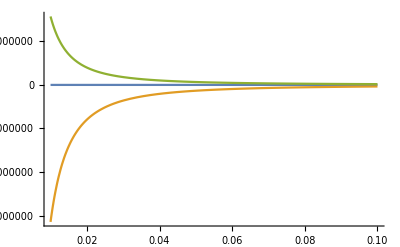

```mathematica
Plot[{dtSum[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1], dtVirtualRight[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1], dtRealRight[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1]},{eps,0.01,0.1},PlotRange->All]
```

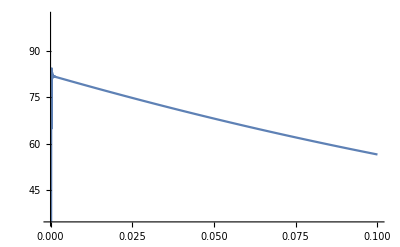

```mathematica
Plot[{dtSum[0.3,0.3,0.3,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1]},{eps,0.0,0.1}]
```

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Causal flow

#### Flow solutions

```mathematica
usualtTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]-norm[{0,lx,ly,lz}])

weirdtTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}])
```

#### Dirac delta jacobians

```mathematica
usualDiracJTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[-norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}+{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

weirdDiracJTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Usual Cut

-Graphics-

```mathematica
usualCut[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0+p10+p20) 2(l0+k0)] SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}] })
```

```mathematica
usualCut[kx,ky,kz,lx,ly,lz,1,0,0,1,0,0,-1];
```

```mathematica
usualCutLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0+p10+p20) 2(l0+k0)] SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}] })
```

### Weird Cut 1

This is the true and unique ISR singularity

-Graphics-

```mathematica
weirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=-((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2l0 2(k0+p10+p20) 4(k0)^3 ]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((1/Abs[2l0 2(k0+p10+p20) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0}]),p0])/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{p0->0}
```

```mathematica
weirdCut1LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2l0 2(k0+p10+p20) 4(k0)^3 ]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]))/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((1/Abs[2l0 2(k0+p10+p20) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0}]),p0])/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{p0->0}
```

### Weird Cut 2

This one is a diagram without support, and should not be included ultimately.Indeed, there is no such singularity in the original diagram (once energy conservation is applied)

-Graphics-

```mathematica
weirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2(k0+l0) 2(k0+p10+p20) 4(k0)^3 ]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->-k0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}]}/.{k0->-norm[{0,kx,ky,kz}]})-
(((1/Abs[2norm[{0,kx,ky,kz}+{0,lx,ly,lz}] 2(k0+p10+p20) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(SP[{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz}]),p0])/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{p0->0})
```

#### Numerator cancellation

It seems that, even without considering the fact that the singularity has no support, it wouldn' t be there to begin with, because the numerator exactly vanishes at the location of the singularity

```mathematica
testf[x_,y_]:=Simplify[(twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->-k0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}]}/.{k0->-norm[{0,kx,ky,kz}]})/.{p10->1,p1x->0,p1y->0,p1z->1,p2x->0,p2y->0,p2z->-1,kx->0,ky->0,kz->-x,lx->0,ly->0,lz->y}]
```

```mathematica
testf[0.3,1]
```

0.

### Cross section per supergraph

#### Toy model

```mathematica
twoSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=usualCut[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+weirdCut1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+weirdCut2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

#### LU

```mathematica
tChLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,rt,sum,c},
vt=usualtTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rt=weirdtTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*Print[vt];*)
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=( vt^6(Exp[-vt^2/sigma^2])/(usualDiracJTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rt^6(Exp[-rt^2/sigma^2])/(weirdDiracJTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);
(*
If[DEBUG,
Print["virtual: "];Print[vt^6(Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];Print[rt^6(Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
];*)

c*sum
];
```

```mathematica
weirdtChLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{rt,sum,c},
rt=weirdtTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*Print[vt];*)
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=rt^6(Exp[-rt^2/sigma^2])/(weirdDiracJTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*
If[DEBUG,
Print["virtual: "];Print[vt^6(Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];Print[rt^6(Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
];*)

c*sum
];
```

```mathematica
usualtChLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,sum,c},
vt=usualtTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*Print[vt];*)
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=( vt^6(Exp[-vt^2/sigma^2])/(usualDiracJTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);
(*
If[DEBUG,
Print["virtual: "];Print[vt^6(Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];Print[rt^6(Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
];*)

c*sum
];
```

```mathematica
tChLU[0,0.2,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.2,False]
```

-1.52736×10^-34+0. ⅈ

#### Cancellations for the LU expression

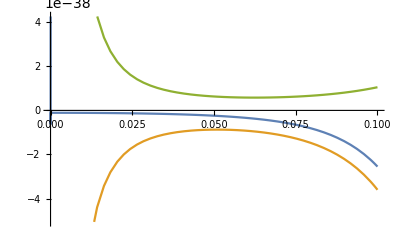

```mathematica
Plot[{tChLU[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.2,False],weirdtChLU[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.2,False],usualtChLU[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.2,False]},{eps,0,0.1}]
```

General::munfl: Exp[-1.01285×10^16] is too small to represent as a normalized machine number; precision may be lost.

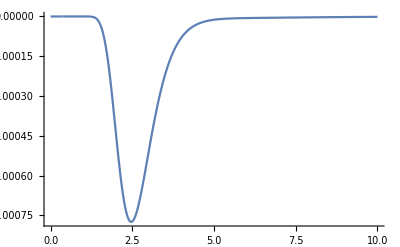

840002.

```mathematica
Plot[tChLU[0,eps,-0.3,0,0,1,1,0,0,1,1,0,0,-1,0.2,False],{eps,0,10},PlotRange->All]
usualtTch[0,0.001,-0.3,0,0,1,1,0,0,1,1,0,0,-1]
```

#### Integration test for LU expression

```mathematica
Table[NIntegrate[tChLU[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,1,False],{kx,-2,2},{ky,-2,2},{kz,-2,2},{lx,-2,2},{ly,-2,2},{lz,-2,2},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->1000000,MaxRecursion->1000],{i,1,5}]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 547.445+0. ⅈ and 2.2422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 548.993+0. ⅈ and 2.22796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 553.557+0. ⅈ and 2.3326 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{547.445,548.993,553.557,561.439,536.968}

### Ir limits

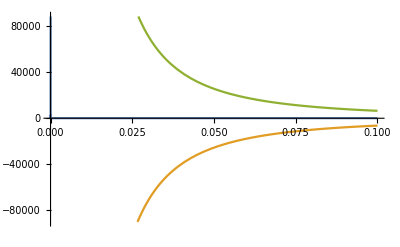

```mathematica
Plot[{weirdCut1[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1]+usualCut[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1],usualCut[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1],weirdCut1[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

Look at Weird Cut 2 cancellation folder for explanation of the absence of the following singularity

```mathematica
den[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(1/SP[{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz}])/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{p0->0}
```

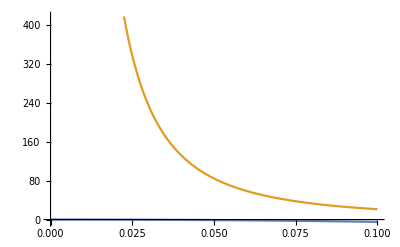

```mathematica
Plot[{weirdCut2[0,eps,-0.3,0,0,1,1,0,0,1,0,0,-1]+usualCut[0,eps,-0.3,0,0,1,1,0,0,1,0,0,-1],den[0,eps,-0.3,0,0,1,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

## -Graphics-

### Usual cut

-Graphics-

```mathematica
uChannelUsualCut[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+l0)2(k0+p10+p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelUsualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

```mathematica
uChannelUsualCutLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+l0)2(k0+p10+p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Weird cut 1

-Graphics-

```mathematica
uChannelWeirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2k0 2(k0+p10+p20)]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelWeirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

```mathematica
uChannelWeirdCut1LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2k0 2(k0+p10+p20)]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Weird Cut 2

-Graphics-

```mathematica
uChannelWeirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+l0)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-l0-k0-norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelWeirdCut2[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

```mathematica
uChannelWeirdCut2LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+l0)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Cross section per supergraph

```mathematica
uChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=uChannelUsualCut[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+uChannelWeirdCut1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+uChannelWeirdCut2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

### Ir limits

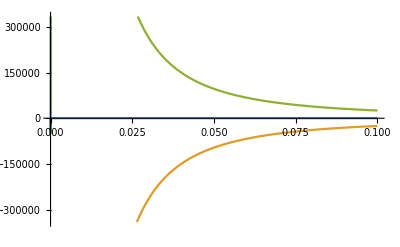

```mathematica
Plot[{uChannelWeirdCut1[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1]+uChannelUsualCut[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1],uChannelUsualCut[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1],uChannelWeirdCut1[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

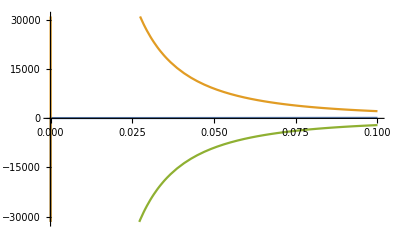

```mathematica
Plot[{uChannelWeirdCut2[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1]+uChannelUsualCut[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1],uChannelWeirdCut2[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1],uChannelUsualCut[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

## -Graphics-

### Only cut

This diagram has no singularities

```mathematica
sChannelBub[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((sChannelBubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2 (k0+p10+p20-l0)2 k0] SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^2))/.{p20->-p10+l0-k0+norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}-{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

sChannelBub[kx,ky,kz,lx,ly,lz,1,0,0,1,0,0,-1];
```

```mathematica
sChannelBubLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((sChannelBubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2 (k0+p10+p20-l0)2 k0] SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^2))/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

```mathematica
sChannelBubLU[1,2,3,4,5,6,1,0,0,1,1,0,0,-1];
```

### Cross section per supergraph

```mathematica
sChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=sChannelBub[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Causal flow

#### Flow Solutions

```mathematica
rSolBub[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
vSolBub[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
```

#### Dirac Delta Jacobians

```mathematica
rSolBubDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
vSolBubDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}],{sx,sy,sz}]/.{sx->kx,sy->ky,sz->kz};
```

### Real cut

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
bdReal[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0-l0)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->l0+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

LU version (on - shell energy delta not yet solved)

```mathematica
bdRealLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0-l0)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{k0->p10+p20-norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Virtual cut

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
bdVirtual[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(D[((bubNumerator[{k0,kx,ky,kz},{norm[{0,lx,ly,lz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2norm[{0,lx,ly,lz}]]SP[{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz},{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz}]))+(bubNumerator[{k0,kx,ky,kz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2 norm[{0,lx,ly,lz}-{0,kx,ky,kz}]]SP[{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz}]))),p0]/.{p0->0}/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
bdVirtual[kx,ky,kz,lx,ly,lz,1,0,0,1,0,0,-1];
```

LU version (on - shell energy delta not yet solved)

```mathematica
bdVirtualLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(D[((bubNumerator[{k0,kx,ky,kz},{norm[{0,lx,ly,lz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2norm[{0,lx,ly,lz}]]SP[{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz},{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz}]))+(bubNumerator[{k0,kx,ky,kz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2 norm[{0,lx,ly,lz}-{0,kx,ky,kz}]]SP[{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz}]))),p0]/.{p0->0}/.{k0->p10+p20-norm[{0,kx,ky,kz}]})
bdVirtualLU[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1];
```

### Cross section per supergraph

#### Toy model

```mathematica
bubbleSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=bdReal[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+bdVirtual[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z];
```

#### LU

```mathematica
bubLUrep[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,rt,sum,c},
rt=rSolBub[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
vt=vSolBub[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c=const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

Print[{vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz}];

sum=( vt^6(Exp[-vt^2/sigma^2])/(vSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdVirtualLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rt^6(Exp[-rt^2/sigma^2])/(rSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdRealLU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

If[DEBUG,
Print["virtual: "];
Print[c vt^6(Exp[-vt^2/sigma^2])/(vSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdVirtualLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];
Print[c rt^6(Exp[-rt^2/sigma^2])/(rSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdRealLU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];];

c*sum
];
```

#### LU expression test

```mathematica
bubLUrep[-0.0201817368890378,0.06211299937499417,0.08989077715277194,-0.5393446629166317,-0.39185683486164874,0,1,0,0,1,1,0,0,-1,2,True]
Print["-----------"]
Print["virtual benchmark: "];
Print["-0.0000294636"];
Print["real benchmark: "];
Print["4.001390989976316`"];
```

{-0.181636,0.559017,0.809017,-4.8541,-3.52671,0.}

virtual:

0.-0.0000294636 ⅈ

real:

0.+4.00139 ⅈ

0.+4.00136 ⅈ

-----------

virtual benchmark:

-0.0000294636

real benchmark:

4.001390989976316`

### Ir limits

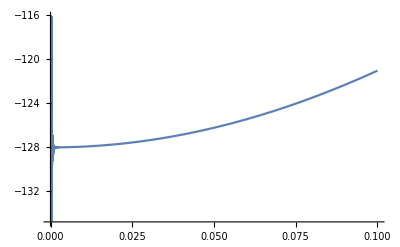

```mathematica
Plot[{bubbleSum[0,eps,1,0,0,0.5,1,0,0,1,0,0,-1],bdVirtual[0,eps,1,0,0,0.5,0,0,0,1,1], bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]},{eps,0,0.1}]
```

## -Graphics-

### Usual cut

Numerator eliminates a singularity

```mathematica
usualSTCut[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0+l0+p10+p20)2l0]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-k0-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->-norm[{0,kx,ky,kz}]})

usualSTCut[0,0.00000001,-0.5,0,0,1,1,0,0,1,0,0,-1];
```

```mathematica
usualSTCutLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0+l0+p10+p20)2l0]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{l0->norm[{0,lx,ly,lz}]}/.{k0->-norm[{0,kx,ky,kz}]})
```

### Weird cut 1

This one is a diagram without support, and should not be included ultimately. Indeed, there is no such singularity in the original diagram (once energy conservation is applied)

```mathematica
weirdSTCut1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0+p10+p20)2(k0+l0+p10+p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{l0->-k0-p10-p20+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]})

weirdSTCut1[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

```mathematica
weirdSTCut1LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0+p10+p20)2(k0+l0+p10+p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{l0->-k0-p10-p20+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]})
```

#### Numerator cancellation

It seems that, even without considering the fact that the singularity has no support, it wouldn' t be there to begin with, because the numerator exactly vanishes at the location of the singularity

```mathematica
funct[x_,y_]:=Simplify[(twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/.{p20->-p10-k0-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->-norm[{0,kx,ky,kz}]})/.{p10->1,p1x->0,p1y->0,p1z->1,p2x->0,p2y->0,p2z->-1,kx->0,ky->0,kz->-x,lx->0,ly->0,lz->y}];

funct[0.5,1]
funct[-0.5,1]
```

### Weird cut 2

This is the true and unique ISR singularity

```mathematica
weirdSTCut2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+p10+p20) 2 k0]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}] SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-k0+norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

v2WeirdCut2[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

```mathematica
weirdSTCut2LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+p10+p20) 2 k0]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}] SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{k0->-norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Cross section per supergraph

```mathematica
stChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=v2UsualCut[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+v2WeirdCut1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+v2WeirdCut2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

### Ir limits

Look at Weird Cut 1 cancellation folder for explanation of the absence of the following singularity

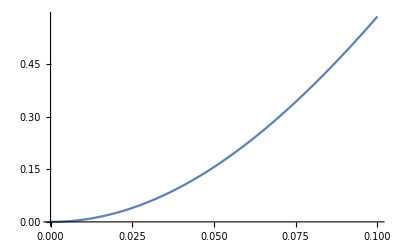

```mathematica
Plot[{usualSTCut[0,eps,-0.5,0,0,1,1,0,0,1,0,0,-1]+weirdSTCut1[0,eps,-0.5,0,0,1,1,0,0,1,0,0,-1](*, bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```

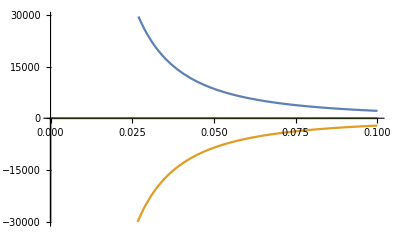

```mathematica
Plot[{usualSTCut[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1],weirdSTCut2[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1],usualSTCut[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1]+weirdSTCut2[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1](*, bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```